# Hurricanes in the XXI century

David Torres

Weather forecasting has been significantly improved during the past century. On the other hand, climate prediction is still unclear and, therefore, we should take precautions and get ready for “surprises”. Our rapid urbanization signals that we are willing to take a lot of risk or that we are not paying enough attention. 

Let’s analyze the case of hurricanes in the XXI century.  First, we should do a list of their names.

```mathematica
Hurricanes2000To2018=Table[EntityList[EntityClass["TropicalStorm","Hurricanes"<>ToString[year]]],{year,2000,2018}]//Short
```

{{Aletta,Carlotta,Daniel,Alberto,Gilma,Hector,Debby,Lane,Florence,Gordon,Isaac,Joyce,Keith,Michael},{Adolph,Dalila,Flossie,Erin,Gil,Felix,Gabrielle,Juliette,Kiko,Humberto,Iris,Karen,Narda,Michelle,Octave,Noel,Olga},«16»,{Alberto,Aletta,Beryl,Bud,Carlotta,Chris,Daniel,Debby,Emilia,Ernesto,Fabio,Florence,Gilma,Gordon,Hector,Helene,Ileana,Isaac,John,Joyce,Kirk,Kristy,Lane,Leslie,Michael,Miriam,Nadine,Norman,Olivia,Oscar,Paul,Rosa,Sergio,Tara,Vicente,Willa,Xavier}}

Second, let’s use their wind speed as a proxy of their magnitude.

```mathematica
WindSpeed2000To2018=Map[#[EntityProperty["TropicalStorm","WindSpeed"]]&,Hurricanes2000To2018,{2}]//Short
```

{{Aletta,Carlotta,Daniel,Alberto,Gilma,Hector,Debby,Lane,Florence,Gordon,Isaac,Joyce,Keith,Michael}[wind speed],«17»,{Alberto,Aletta,Beryl,Bud,Carlotta,Chris,Daniel,Debby,Emilia,Ernesto,Fabio,Florence,Gilma,Gordon,Hector,Helene,Ileana,Isaac,John,Joyce,Kirk,Kristy,Lane,Leslie,Michael,Miriam,Nadine,Norman,Olivia,Oscar,Paul,Rosa,Sergio,Tara,Vicente,Willa,Xavier}[wind speed]}

Third, we can take a more graphical look.

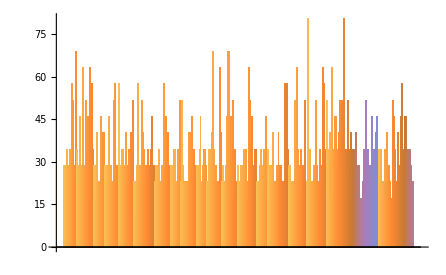

```mathematica
BarChart[WindSpeed2000To2018]
```

Fourth, we can also group the hurricanes per year and have a more clear view.

```mathematica
NumberOfHurricanes2000To2018=Length/@Hurricanes2000To2018
```

{14,17,12,14,16,22,16,11,16,11,15,17,20,11,22,19,20,54,37}

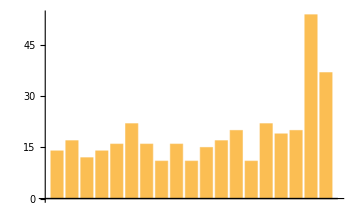

```mathematica
BarChart[NumberOfHurricanes2000To2018]
```

Fifth,  we could also see the higher values or stronger hurricanes for each year.

```mathematica
MaxWindSpeed2000To2018=Max@@@HurricaneSpeeds2000To2018
```

{69.0468 mi/h,63.2929 mi/h,46.0312 mi/h,57.539 mi/h,57.539 mi/h,57.539 mi/h,57.539 mi/h,51.7851 mi/h,51.7851 mi/h,46.0312 mi/h,69.0468 mi/h,69.0468 mi/h,63.2929 mi/h,46.0312 mi/h,57.539 mi/h,63.2929 mi/h,80.5546 mi/h,81. mi/h,57.539 mi/h}

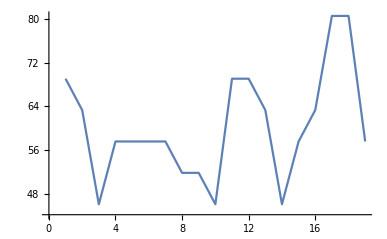

```mathematica
ListLinePlot[MaxWindSpeed2000To2018]
```

Finally, what this increase in the intensity of extreme events like hurricanes represent for society? well that depend’s on the location of the events and what is at risk. In coastal areas where most of the big cities are, the stakes are really high and growing.

```mathematica
Interpreter["Image"][Import["/Users/davidtorres/Desktop/aaa5.png"]]
```

-Graphics-